```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["output"]
```

C:\Users\Ronak\Dropbox\BridgeToIsland\paper\code\output

Remember to search and replace E -> *10^, e -> *10^ in data files before running below block

```mathematica
angles=Table[1,{i,4}];
angles⟦1⟧=ReadList["angles-1em5.txt"];
angles⟦2⟧=ReadList["angles-1em4.txt"];
angles⟦3⟧=ReadList["angles-1em3.txt"];
angles⟦4⟧=ReadList["angles-1em2.txt"];
sps=ReadList["sprime.txt"];(*This is 𝔰'(ζ)*)
schwTerm=ReadList["energy-terms.txt"];
```

```mathematica
pos=Table[-π/2+(π i)/2000,{i,0,2000-1}];
```

```mathematica
πn=1.0*π
```

3.14159

```mathematica
μ=0.4837854589664;
τ=Log[1/μ]
anglesAnalytic=(If[#>0,π+τ/π Log[Tan[#/2]],-π+τ/π Log[Tan[(π+#)/2]]])&/@pos;
```

0.726114

```mathematica
ListPlot[{{pos,angles⟦4⟧}ᵀ,{pos,angles⟦3⟧}ᵀ,{pos,angles⟦2⟧}ᵀ,{pos,angles⟦1⟧}ᵀ,{pos,anglesAnalytic}ᵀ},AxesOrigin->{-πn/2,-πn},AxesLabel-> (Style[#,FontSize->16]&/@{"𝔰","ζ"}),PlotLegends->{"2δ=10^-5","2δ=10^-4","2δ=10^-3","2δ=10^-2","ζ=π+0.726114/πLog[Tan[𝔰/2]]"},PlotTheme->"Classic"]//Rasterize
```

-Graphics-

```mathematica
(*The actual energy*)
energies=(((4.5 π^2)/Log[.483]^2+1/2-#⟦1⟧)1/(#⟦2⟧)^2-2)&/@({schwTerm,sps}ᵀ);
```

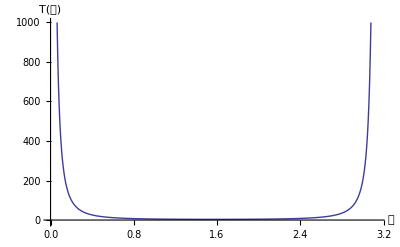

```mathematica
ListPlot[{{pos⟦1001;;2000⟧,energies⟦1001;;2000⟧//Re}ᵀ,{π+pos⟦1;;1000⟧,energies⟦1;;1000⟧//Re}ᵀ}//Flatten[#,1]&,Joined->True,AxesLabel->(Style[#,FontSize->16]&/@{"𝔰","T(𝔰)"}),PlotTheme->"Classic",PlotRange->{{0,π},{-10,1000}},Joined->True]
```

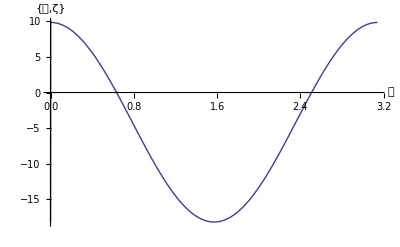

```mathematica
ListPlot[{{pos⟦1001;;2000⟧,schwTerm⟦1001;;2000⟧//Re}ᵀ,{π+pos⟦1;;1000⟧,schwTerm⟦1;;1000⟧//Re}ᵀ}//Flatten[#,1]&,Joined->True,AxesLabel->(Style[#,Bold,FontSize->16]&/@{"𝔰","{𝔰,ζ}"}),PlotTheme->"Classic"(*,PlotRange->{{0,π},{-10,1000}}*),Joined->True]
```